Fechas y horas

En Wolfram Language, Now proporciona la fecha y hora actuales.

Obtenga la fecha y hora actuales (¡de cuando se escribió esto!):

```mathematica
Now
```

Fri 17 Mar 2017 13:39:00GMT-5.

Se pueden hacer cálculos al respecto, por ejemplo, añadir una semana.

Añada una semana a la fecha y hora actuales:

```mathematica
Now+LinguisticAssistant
```

Fri 24 Mar 2017 13:39:00GMT-5.

Se usa ctrl= para ingresar una fecha en cualquier formato estándar.

Ingrese una fecha:

```mathematica
LinguisticAssistant
```

Day: Thu 23 Jun 1988

Puede hacerse aritmética con fechas, por ejemplo, restar una de otra para saber qué tan distantes se encuentran.

Reste una fecha de otra:

```mathematica
Now-LinguisticAssistant
```

10494. days

Convierta la diferencia de fechas en años:

```mathematica
UnitConvert[Now-LinguisticAssistant,"Years"]
```

28.7507 yr

DayRange es el análogo de Range para fechas:

Proporcione una lista de los días que van de ayer a mañana:

```mathematica
DayRange[Yesterday,Tomorrow]
```

{Day: Thu 16 Mar 2017,Day: Fri 17 Mar 2017,Day: Sat 18 Mar 2017}

DayName encuentra el día de la semana para una fecha dada.

Encuentre en qué día de la semana cae el que está a 45 días después de hoy:

```mathematica
DayName[Today+LinguisticAssistant]
```

Monday

Una vez que se conoce una fecha, pueden hacerse una variedad de cosas con ella. Por ejemplo, MoonPhase da la fase de la luna (o, más precisamente, la fracción de la luna que está iluminada cuando se ve desde la Tierra).

Obtenga la fase de la luna en este momento:

```mathematica
MoonPhase[Now]
```

0.7606

Obtenga la fase de la luna en una fecha dada:

```mathematica
MoonPhase[LinguisticAssistant]
```

0.5756

Genere un ícono para la fase de la luna:

```mathematica
MoonPhase[LinguisticAssistant,"Icon"]
```

-Graphics-

Si se conoce la fecha y una ubicación en la Tierra, pueden calcularse las horas de salida y puesta del sol.

Obtenga la hora de la puesta del sol hoy, en la ubicación actual:

```mathematica
Sunset[Here,Today]
```

Minute: Fri 17 Mar 2017 19:04GMT-5.

Obtenga el tiempo transcurrido entre sucesivas horas de salida del sol:

```mathematica
Sunrise[Here,Tomorrow]-Sunrise[Here,Today]
```

1438 min

Se encuentra que la diferencia es casi exactamente un día (24 horas); menos un minuto de variación:

```mathematica
Sunrise[Here,Tomorrow]-Sunrise[Here,Today]-LinguisticAssistant
```

-2 min

Las zonas horarias son una de las muchas sutilezas. LocalTime da la hora en la zona horaria de una ubicación determinada.

Encuentre la hora local actual en la ciudad de Nueva York:

```mathematica
LocalTime[LinguisticAssistant]
```

Fri 17 Mar 2017 14:44:22GMT-4.

Encuentre la hora local actual en Londres:

```mathematica
LocalTime[LinguisticAssistant]
```

Fri 17 Mar 2017 18:44:29GMT

El clima es una de las muchas áreas donde Wolfram Language tiene un amplio espectro de información. La función AirTemperatureData permite dar un historial de la temperatura del aire a cierta hora en alguna ubicación dada.

Encuentre la temperatura del aire aquí, a las 6 p. m. de ayer:

```mathematica
AirTemperatureData[Here,LinguisticAssistant]
```

39.92 °F

Dadas dos fechas, AirTemperatureData calcula una serie cronológica de las temperaturas estimadas entre esas dos fechas.

Proporcione una serie cronológica de mediciones de temperatura del aire desde hace una semana hasta hoy:

```mathematica
AirTemperatureData[Here,{LinguisticAssistant,Now}]
```

TimeSeries[…]

DateListPlot es el análogo de ListPlot para series cronológicas, donde cada valor ocurre en una fecha particular.

Muestre la lista de mediciones de la temperatura del aire:

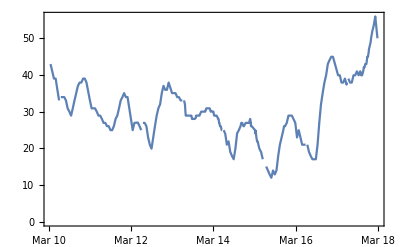

```mathematica
DateListPlot[AirTemperatureData[Here,{LinguisticAssistant,Now}]]
```

No es de sorprender que la temperatura sea más alta durante el día que durante la noche, según se muestra en la gráfica.

Un ejemplo más, con datos que cubren períodos de tiempo mucho más antiguos. WordFrequencyData dice con qué frecuencia aparece una palabra dada, por ejemplo, en una muestra de libros publicados en un año determinado. Se puede tener una amplia visión histórica observando los cambios al respecto en el transcurso de años y siglos.

Encuentre la serie cronológica de la frecuencia con la que aparece en inglés la palabra “automobile”:

```mathematica
WordFrequencyData["automobile","TimeSeries"]
```

TimeSeries[…]

Los coches comenzaron a existir alrededor de 1900, pero gradualmente dejó de llamárseles “automobiles”:

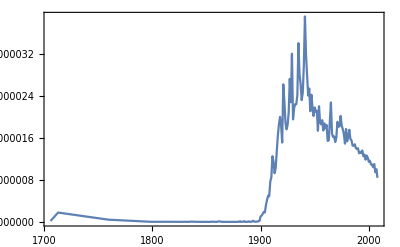

```mathematica
DateListPlot[WordFrequencyData["automobile","TimeSeries"]]
```

WordFrequencyData está hecho de tal modo que facilita la comparación de frecuencias entre diferentes palabras. Por ejemplo, puede verse cómo se han comportado, en ese sentido, los términos “monarchy” y “democracy” a lo largo de los años. “Democracy” es decididamente más popular en la actualidad, pero “monarchy” lo era en los años 1700s y 1800s.

Compare los historiales de las frecuencias de palabras “monarchy” y “democracy”:

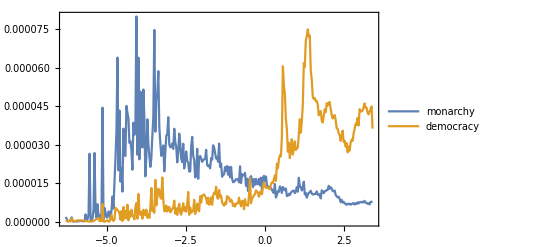

```mathematica
DateListPlot[WordFrequencyData[{"monarchy","democracy"},"TimeSeries"]]
```

Vocabulario

Now |   | fecha y hora actuales
Today |   | objeto que se refiere al día de hoy 
Tomorrow |   | objeto que se refiere al día de mañana
Yesterday |   | objeto que se refiere al día de ayer 
DayRange[fecha_1,fecha_2] |   | lista de fechas entre fecha_1 y fecha_2
DayName[fecha] |   | día de la semana correspondiente a fecha
MoonPhase[fecha] |   | fase de la luna en fecha 
Sunrise[ubicación,fecha] |   | hora de salida del sol en fecha, en ubicación
Sunset[ubicación,fecha] |   | hora de la puesta del sol en fecha, en ubicación
LocalTime[ubicación] |   | hora actual en ubicación 
AirTemperatureData[ubicación,time] |   | temperatura del aire a la hora time, en ubicación 
AirTemperatureData[ubicación,{hora_1,hora_2}] |   | serie cronológica de temperaturas del aire 
entre hora_1 y hora_2, en ubicación 
DateListPlot[seriecronológica] |   | presenta gráficamente una serie cronológica 
WordFrequencyData["palabra","TimeSeries"] |   | serie cronológica de frecuencias de palabra

"13 Exercises Available"
"with 7 extras" | "Get Started »"

Calcule cuántos días han transcurrido desde el 1 de enero de 1900. »

| Sample expected output: |  
  | 42809. "days" |

Determine qué día de la semana fue el 1 de enero de 2000. »

| Sample expected output: |  
  | Saturday |

Encuentre la fecha de hace cien mil días. »

| Sample expected output: |  
  | "Sun 2 Jun 1743 14:40:00""GMT"-5. |

Encuentre la hora local en Delhi. »

| Sample expected output: |  
  | "Fri 17 Mar 2017 01:15:29""GMT+"5.5 |

Encuentre la duración de luz solar hoy, restando la hora de la salida del sol de la hora de la puesta. »

| Sample expected output: |  
  | -717 "min" |

Genere un ícono de la fase actual de la luna. »

| Sample expected output: |  
  |  |

Haga una lista de la fase numérica de la luna para cada uno de los próximos 10 días. »

| Sample expected output: |  
  | {0.6748,0.5837,0.489,0.3932,0.2994,0.2112,0.1326,0.06838,0.02335,0.001956} |

Genere una lista de íconos de las fases de la luna para los próximos 10 días, a partir de hoy. »

| Sample expected output: |  
  | {,,,,,,,,,} |

Calcule el tiempo transcurrido entre las horas de salida del sol en Nueva York y en Londres. »

| Sample expected output: |  
  | 294 "min" |

Encuentre la temperatura del aire en la Torre Eiffel ayer a mediodía. »

| Sample expected output: |  
  | 64.94 "°F" |

Grafique la temperatura del aire en la Torre Eiffel durante la semana pasada. »

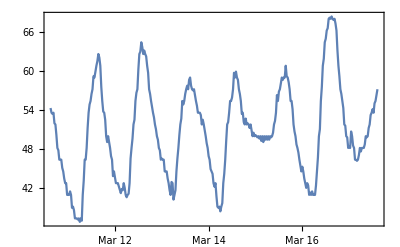
| Sample expected output: |  
  | -Graphics- |

Encuentre la diferencia en temperatura del aire entre Los Ángeles y Nueva York, ahora. »

| Sample expected output: |  
  | 19.08 "°F" |

Grafique el historial de las frecuencias de la palabra “groovy”. »

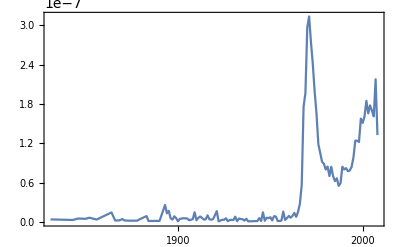
| Expected output: |  
  | -Graphics- |

Calcule cuántas semanas han transcurrido desde el 1 de enero de 1900. »

| Expected output: |  
  | 6115.57 "wk" |

Calcule el tiempo entre las 3 p. m. de hoy y la hora de salida del sol, el día de hoy. »

| Expected output: |  
  | 4. "h" |

Genere un ícono de la fase de la luna del 29 de agosto de 1959. »

| Expected output: |  
  |  |

Haga una gráfica con los puntos unidos de la fase numérica de la luna, para cada uno de los próximos 30 días. »

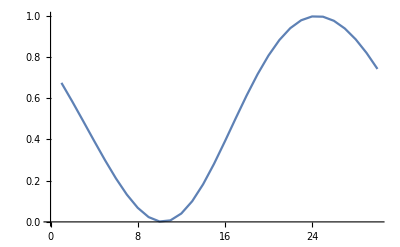
| Expected output: |  
  | -Graphics- |

Haga un Manipulate del ícono de la fase de la luna para los próximos 15 días. »

| Expected output: |  
  |  |

Muestre en una columna las horas de salida del sol para los próximos 10 días a partir de hoy. »

| Expected output: |  
  | "Minute: ""Sat 18 Mar 2017 07:00""GMT"-5.
"Minute: ""Sun 19 Mar 2017 06:59""GMT"-5.
"Minute: ""Mon 20 Mar 2017 06:57""GMT"-5.
"Minute: ""Tue 21 Mar 2017 06:56""GMT"-5.
"Minute: ""Wed 22 Mar 2017 06:54""GMT"-5.
"Minute: ""Thu 23 Mar 2017 06:52""GMT"-5.
"Minute: ""Fri 24 Mar 2017 06:51""GMT"-5.
"Minute: ""Sat 25 Mar 2017 06:49""GMT"-5.
"Minute: ""Sun 26 Mar 2017 06:47""GMT"-5.
"Minute: ""Mon 27 Mar 2017 06:46""GMT"-5. |

Grafique conjuntamente la frecuencia histórica de las palabras “science” y “technology”. »

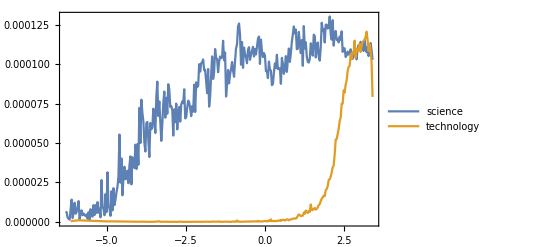
| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Cómo se convierte una fecha a una cadena de caracteres?

Use DateString[fecha]. Hay diversas opciones para el formato de la cadena. Por ejemplo, DateString[fecha,"DateShort"] usa las abreviaturas para los nombres de día y mes.

¿Cómo extraer el mes o algún otro elemento de una fecha?

Use DateValue. DateValue[fecha,"Month"] da el número del mes, DateValue[fecha,"MonthName"] da el nombre del mes, etc.

¿Qué tan antiguas pueden ser las fechas en Wolfram Language?

Tanto como se desee. Wolfram Language tiene conocimiento de los sistemas de calendario históricos y de la historia de las zonas horarias. Tiene también información para calcular con precisión las horas de salida del sol, etc. desde 1 000 años atrás.

¿Por qué las horas de salida y puesta del sol se dan solamente con una precisión de minutos?

Porque no puede calcularse con mayor precisión ni la salida ni la puesta del sol sin conocer datos tales como la temperatura del aire, que afectan la curvatura de la luz en la atmósfera terrestre.

¿De dónde obtiene Wolfram Language la información de la temperatura del aire?

De la red global de estaciones meteorológicas ubicadas en aeropuertos y otros lugares. En caso de que el lector posea su propio instrumento de medición de la temperatura del aire, puede conectarlo a Wolfram Language a través de Wolfram Data Drop (ver la Sección 43).

¿Qué es una serie cronológica?

Es una forma de especificar los valores de algo a lo largo de una serie de instantes en el tiempo. Se puede ingresar una serie cronológica en Wolfram Language como

TimeSeries[{{tiempo_1,valor_1},{tiempo_2,valor2_2},...}]. Wolfram Language permite hacer operaciones aritméticas y de muchos otros tipos con series cronológicas.

¿Qué es lo que hace DateListPlot?

Graficar valores correspondientes a instantes de tiempo o a fechas. Los valores pueden darse en una TimeSeries[...] o en una lista de la forma {{tiempo_1,valor_1},{tiempo_2,valor_2},...}.

Notas técnicas

Wolfram Language decide si hay que interpretar una fecha así: 8/10/15, como mes/día/año o día/mes/año, según el país donde se encuentre. Uno puede escoger la otra interpretación, si así lo desea.

Monday, etc. son símbolos con significado intrínseco, y no cadenas de caracteres.

DateObject permite especificar la «granularidad» de una fecha (día, semana, mes, año, década, etc.). CurrentDate, NextDate, DateWithinQ, etc. operan con fechas granulares.

Se puede ver lo que hay «dentro» de DateObject[...] usando InputForm.

Para explorar más

Guía para fechas y tiempos en Wolfram Language »